## Initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\props.m";
```

## Brachyury Flow

### video B7

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\B7\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg-cropped.tif"][[;;120]];
```

```mathematica
signal=ExtractSignal[images];
inCent=centroidsIntensity@signal;
```

```mathematica
ListAnimate@MapThread[HighlightImage[#1,#2]&,{images,signal}]
```

```mathematica
Rasterize[coloredTraj[inCent,0.1],"Graphics",ImageResolution->200]
```

-Graphics-

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

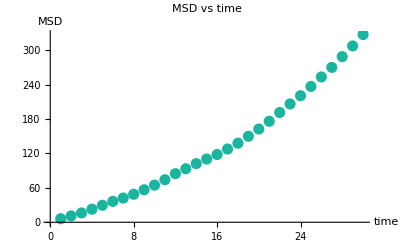

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

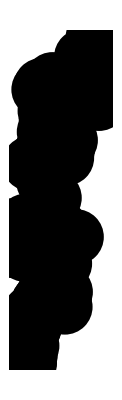

```mathematica
Show[Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.04],Point@movAvg}],coloredTraj[inCent,0.1]]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean[distance]
```

0.957141

```mathematica
dist=FindDistribution[distance]
```

GammaDistribution[3.18479,0.304554]

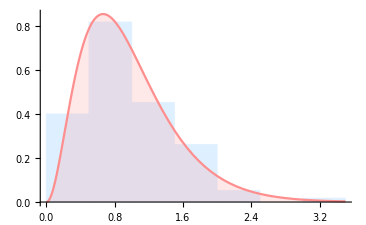

```mathematica
histogramDist[distance,dist,3.5]
```

### video C8

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\C8\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg-cropped.tif"][[;;-12]];
```

```mathematica
signal=ExtractSignal[images];
inCent=centroidsIntensity@signal;
```

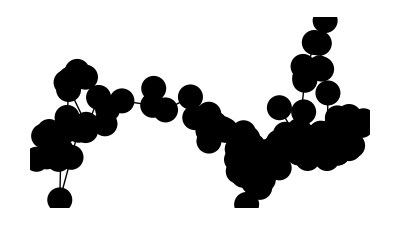

```mathematica
coloredTraj[inCent,0.045]
```

```mathematica
ListAnimate@MapThread[HighlightImage[#1,#2]&,{images,signal}]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

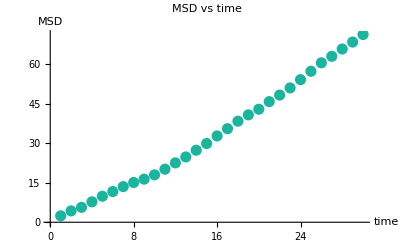

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

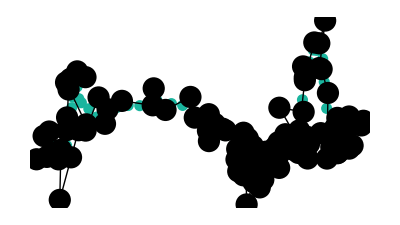

```mathematica
Show[Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.02],Point@movAvg}],coloredTraj[inCent,0.04]]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.52524

```mathematica
dist=FindDistribution[distance]
```

LogNormalDistribution[-0.848925,0.682879]

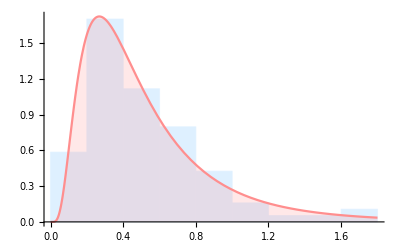

```mathematica
histogramDist[distance,dist,1.8]
```

### video C10

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\C10\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg-cropped.tif"][[;;158]];
```

```mathematica
signal=ExtractSignal[images];
inCent=centroidsIntensity@signal;
```

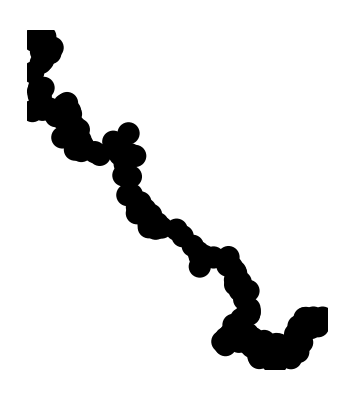

```mathematica
coloredTraj[inCent,0.04]
```

```mathematica
ListAnimate@MapThread[HighlightImage[#1,#2]&,{images,signal}]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

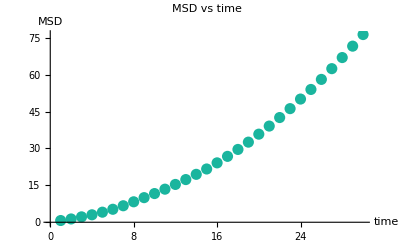

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

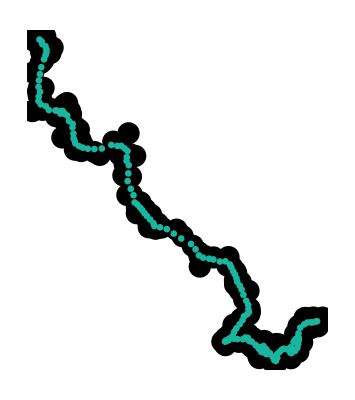

```mathematica
Show[coloredTraj[inCent,0.04],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.012],Point@movAvg}]]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.367491

```mathematica
dist=FindDistribution[distance]
```

GammaDistribution[4.05596,0.0910655]

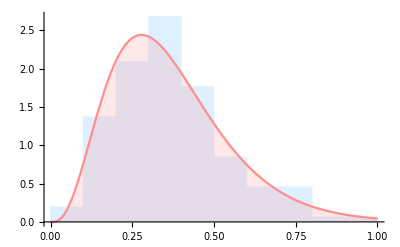

```mathematica
histogramDist[distance,dist]
```

### video D7

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\D7\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg-cropped.tif"][[;;155]];
```

```mathematica
signal=ExtractSignal[images];
inCent=centroidsIntensity@signal;
```

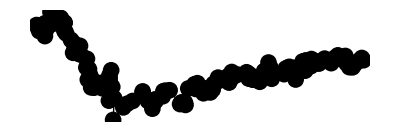

```mathematica
coloredTraj[inCent,0.030]
```

```mathematica
ListAnimate@MapThread[HighlightImage[#1,#2]&,{images,signal}]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

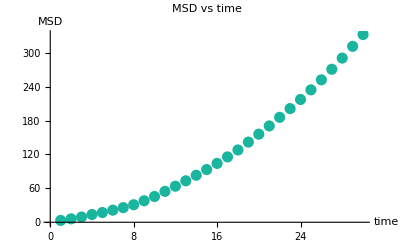

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

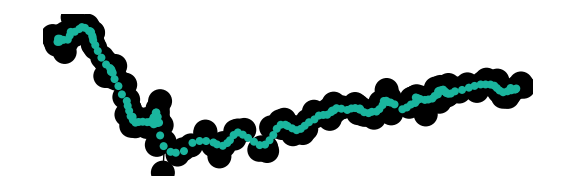

```mathematica
Show[coloredTraj[inCent,0.030],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.01],Point@movAvg}],ImageSize-> Large]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.740273

```mathematica
dist=FindDistribution[distance]
```

RayleighDistribution[0.596369]

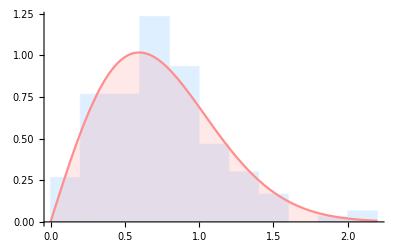

```mathematica
histogramDist[distance,dist,2.2]
```

### video D11

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\D11\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg-cropped.tif"][[;;120]];
```

```mathematica
signal=ExtractSignal[images];
inCent=centroidsIntensity@signal;
```

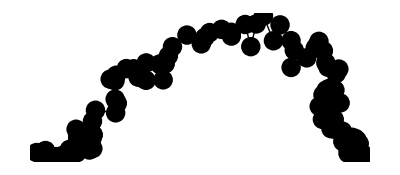

```mathematica
coloredTraj[inCent,0.035]
```

```mathematica
ListAnimate@MapThread[HighlightImage[#1,#2]&,{images,signal}]
```

```mathematica
images~trajVid~inCent
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

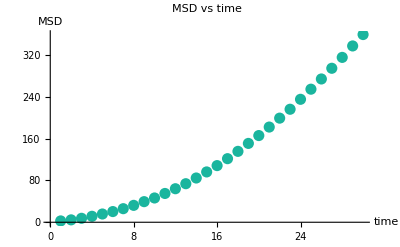

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

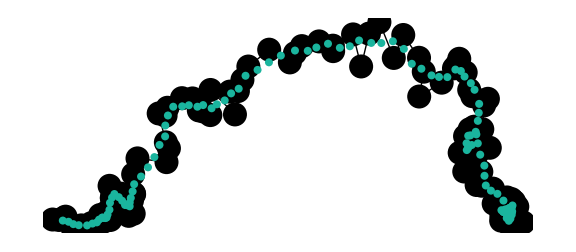

```mathematica
Show[coloredTraj[inCent,0.03],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.01],Point@movAvg}],ImageSize->Large]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
Mean@distance
```

0.684952

```mathematica
dist= FindDistribution[distance]
```

WeibullDistribution[1.64618,0.766124]

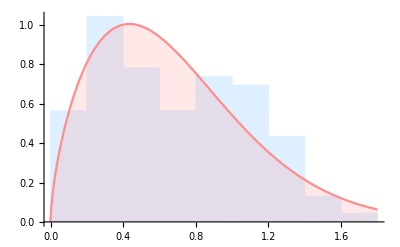

```mathematica
histogramDist[distance,dist,1.8]
```

### video E10

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\E10\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg-cropped.tif"][[;;100]];
```

```mathematica
signal=ExtractSignal[images];
inCent=centroidsIntensity@signal;
```

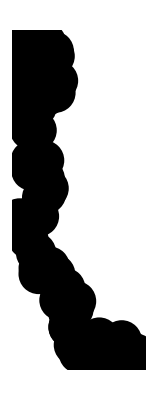

```mathematica
coloredTraj[inCent,0.0725]
```

```mathematica
ListAnimate@MapThread[HighlightImage[#1,#2]&,{images,signal}]
```

```mathematica
trajVid[images,inCent]
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

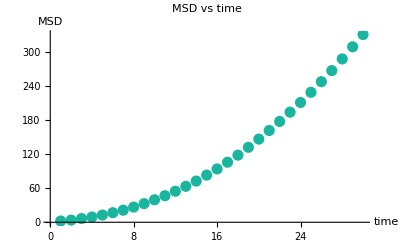

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

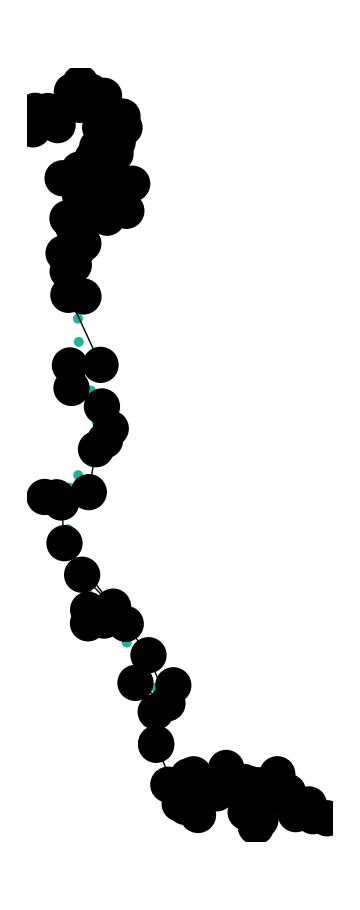

```mathematica
Show[Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.02],Point@movAvg}],coloredTraj[inCent,0.0725], ImageSize->Medium]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
dist=FindDistribution[distance]
```

GammaDistribution[2.5695,0.240366]

```mathematica
Mean@distance
```

0.613937

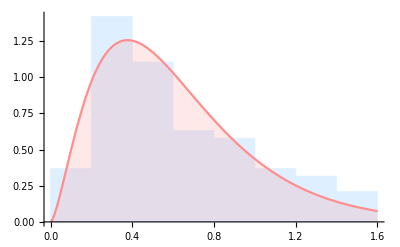

```mathematica
histogramDist[distance,dist,1.6]
```

### video F10

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\F10\\";
images=ImageAdjust/@Import[dir<>"brachyury-Reg-cropped.tif"][[;;150]];
```

```mathematica
signal=ExtractSignal[images];
inCent=centroidsIntensity@signal;
```

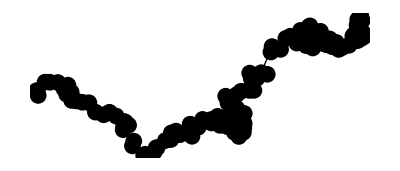

```mathematica
coloredTraj[inCent,0.03]
```

```mathematica
ListAnimate@MapThread[HighlightImage[#1,#2]&,{images,signal}]
```

```mathematica
images~trajVid~inCent
```

```mathematica
msd=MSD[inCent,30,"M2"];
```

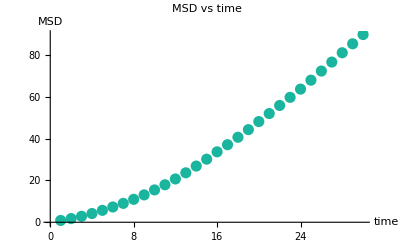

```mathematica
ListPlot[msd,PlotLabel->"MSD vs time",AxesLabel->{"time","MSD"},PlotStyle->{RGBColor[0.1, 0.71, 0.62],PointSize@0.02}]
```

```mathematica
movAvg=MovingAverage[inCent,5];
```

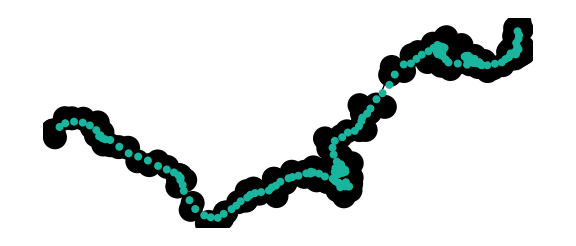

```mathematica
Show[coloredTraj[inCent,0.03],Graphics[{RGBColor[0.1, 0.71, 0.62],PointSize[0.01],Point@movAvg}], ImageSize->Large]
```

```mathematica
distance=EuclideanDistance@@#&/@Partition[movAvg,2,1];
```

```mathematica
dist=FindDistribution[distance]
```

WeibullDistribution[2.01118,0.482618]

```mathematica
Mean@distance
```

0.424968

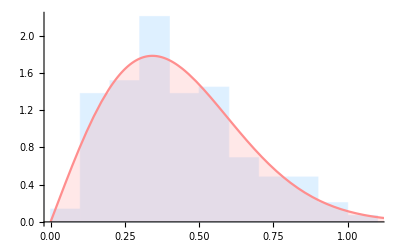

```mathematica
histogramDist[distance,dist,1.2]
```

## MSD plot and velocity distribution

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\Brachyury_motion_1.mx";
```

```mathematica
acquistionPeriod=6;
```

```mathematica
timesteps=Ceiling[0.25(Map[Length]@saved //Mean)]
```

33

```mathematica
msds=MSD[#,timesteps,"M2"]&/@saved;
```

```mathematica
(* since the timelapse images were binned 2x2, acquisition time 6 minutes *)
```

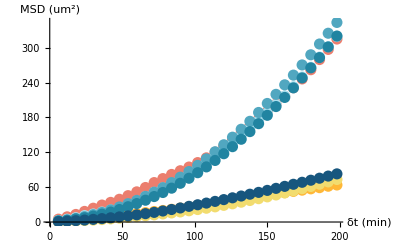

```mathematica
ListPlot[Thread[{Range@Length@# *acquistionPeriod,#*2*(0.633)^2}]&/@msds,PlotStyle->ColorData[24],AxesLabel->{Style["δt (min)",{Bold,15}],
Style["MSD (um^2)",{Bold,15}]},AxesStyle->Directive[Black, 14]]/.PointSize[_]:> PointSize[0.02]
```

```mathematica
velocities= Flatten[EuclideanDistance@@#&/@Partition[#,2,1]&/@saved,1]/acquistionPeriod;
```

```mathematica
dist=FindDistribution@velocities
```

GammaDistribution[1.63354,0.128415]

```mathematica
meanvelocity=Mean[dist]
```

0.20977

```mathematica
Rasterize[histogramDist[velocities,dist,1.3],"Graphics",ImageResolution->500]
```

-Graphics-